## KERNEL-DOCS

## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<Geometry`
```

## Object Specifications

### POINT

```mathematica
POINT
```

0

```mathematica
newGeo[{POINT,{{2,2},{4,4},{0,4}}}];
newGeo[{POINT,{{2,2},{4,4},{0,4}}}]//toGL;
newGeo[{POINT,{{2,2},{4,4},{0,4}}}]//toGL//gr1;

newGeo[{POINT,{{2,2},{4,4},{0,4}}}]//toGL
newGeo[{POINT,{{2,2},{4,4},{0,4}}}]//toGL
```

{RGBColor[1, 0, 0],Opacity[1],{PointSize[0.0125],Point[{{2,2},{4,4},{0,4}}]}}

{RGBColor[1, 0, 0],Opacity[1],{PointSize[0.0125],Point[{{2,2},{4,4},{0,4}}]}}

```mathematica
gPoint[p:pnt]:=newGeo[{POINT,{p}}]
gPoint[p:pts]:=p/.q:pnt:>gPoint[q]
```

{{{{0,{{1,2}}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}},{{{0,{{3,4}}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}}

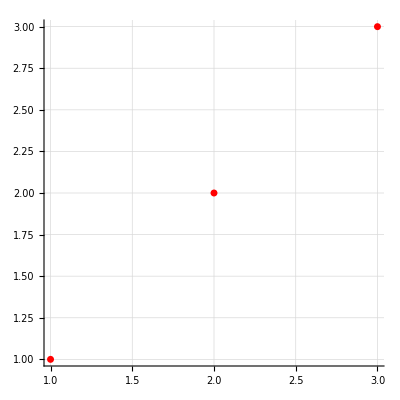

```mathematica
gPoint[{{1,2},{3,4}}]
gPoint[{{1,1},{2,2},{3,3}}]//toGL//gr1
```

### POLYGON

{{{1,{{2,2},{4,4},{0,4}}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}

{RGBColor[1, 0, 0],Opacity[1],{EdgeForm[{GrayLevel[0],Opacity[1],Thickness[0.0125],Dashing[{2 π,2 π}]}],Polygon[…]}}

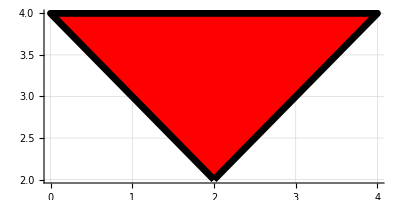

```mathematica
newGeo[{1,{{2,2},{4,4},{0,4}}}]
newGeo[{1,{{2,2},{4,4},{0,4}}}]//toGL
newGeo[{1,{{2,2},{4,4},{0,4}}}]//toGL//gr1
```

### CIRCLE

```mathematica
CIRCLE;
FACE;
EDGE;
newGeo[{CIRCLE,{{2,2},{4,4}}}]//TreeForm;
cCircle[{0,0},1]//toGL//gr1;
newGeo[{CIRCLE,{{2,2},{4,4}}}];


newGeo[{2,{{2,2},{4,4}}}]//toGL//gr1

{{{2,{{2,2},{4,4}}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}//toGL//gr1
```

```mathematica
newGeo[{CIRCLE,{{2,2},{4,4}}}];
newGeo[{CIRCLE,{{2,2},{4,4}}}]//toGL;
newGeo[{CIRCLE,{{2,2},{4,4}}}]//toGL//gr1;
```

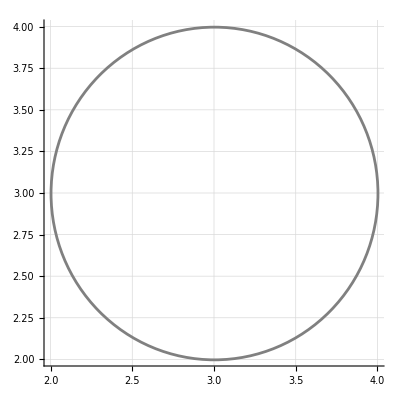

```mathematica
gCircle[2+2I,2 √2];
gCircle[2+2I,2 √2]//toGL;
gCircle[2+2I,2 √2,Color->Blue]//toGL//gr1;
gCircle[I,Color->Gray]//toGL//gr1;
gCircle[{0,1},1,Color->Green]//toGL//gr1;
gCircle[{3,3},Color->Gray, Thickness->0.005]//toGL//gr1
```

### LINE

{{{3,{{2,2},{4,4}}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}

{RGBColor[1, 0, 0],Opacity[1],{GrayLevel[0],Opacity[1],Thickness[0.0125],Dashing[{2 π,2 π}],Line[{{2,2},{4,5}}]}}

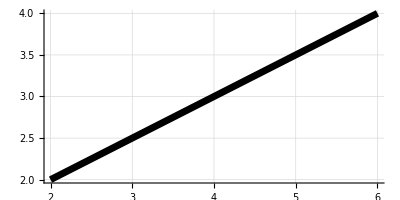

```mathematica
newGeo[{3,{{2,2},{4,4}}}]
newGeo[{3,{{2,2},{4,5}}}]//toGL
newGeo[{3,{{2,2},{4,4}}}]//toGL//gr1;

fig1:=newGeo[{3,{{2,2},{6,4}}}];
fig1//toGL//gr1
```

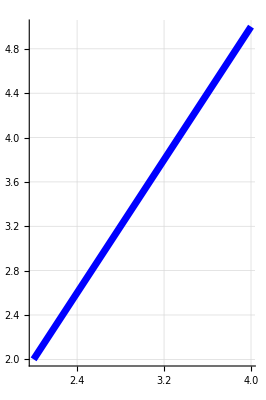

```mathematica
{RGBColor[1, 0, 0],Opacity[1],{Blue,Opacity[1],Thickness[0.0125],Dashing[{2 π,2 π}],Line[{{2,2},{4,5}}]}}//gr1
```

### DISK

{{{4,{{2,2},{4,4}}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}

{RGBColor[1, 0, 0],Opacity[1],{EdgeForm[{GrayLevel[0],Opacity[1],Thickness[0.0125],Dashing[{2 π,2 π}]}],Disk[{2,2},2 √2]}}

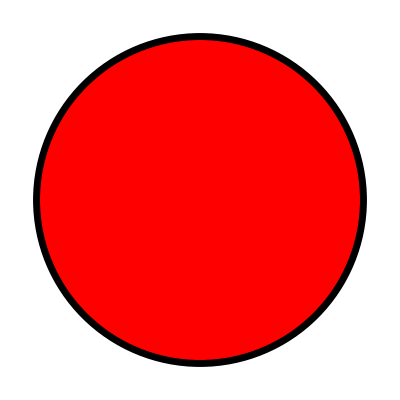

```mathematica
newGeo[{4,{{2,2},{4,4}}}]
newGeo[{4,{{2,2},{4,4}}}]//toGL
newGeo[{4,{{2,2},{4,4}}}]//toGL//gr
```

### FILLEDCURVE

```mathematica
newGeo[{5,{{2,2},{4,4}}}];
newGeo[{5,{{2,2},{4,4}}}]//toGL
newGeo[{5,{{2,2},{3,10},{4,4}}}]//toGL//gr1
```

{RGBColor[1, 0, 0],Opacity[1],{EdgeForm[Directive[{GrayLevel[0],Opacity[1],Thickness[0.0125],Dashing[{2 π,2 π}]}]],FilledCurve[BezierCurve[{{2,2},{4,4}}]]}}

-Graphics-

### HYPERBOLIC LINE

```mathematica
newGeo[{3,{{2,2},{4,4}}}];
newGeo[{6,{{2,2},{4,4}}}]//toGL//gr1
```

LinearSolve::nosol: Linear equation encountered that has no solution.

Part::partw: Part 3 of LinearSolve[{{4,4,-1},{8,8,-1},{1/2,1/2,-1}},{8,32,1/8}] does not exist.

Thread::tdlen: Objects of unequal length in {{{-2,-2,3},{-6,-6,3},{3/2,3/2,3}},{-6,-30,15/8}} {{1/(√(80-LinearSolve[«2»]⟦3⟧)),1/(√(80-LinearSolve[«2»]⟦3⟧)),1/(√(65-LinearSolve[«2»]⟦3⟧))},{1/(√(1088-LinearSolve[«2»]⟦3⟧)),1/(√(1088-LinearSolve[«2»]⟦3⟧)),1/(√(1025-LinearSolve[«2»]⟦3⟧))},{1/(√(17/64-LinearSolve[«2»]⟦3⟧)),1/(√(17/64-LinearSolve[«2»]⟦3⟧)),1/(√(65/64-LinearSolve[«2»]⟦3⟧))}} cannot be combined.

Thread::tdlen: Objects of unequal length in ArcTan[{{{-2,-2,3},{-6,-6,3},{3/2,3/2,3}},{-6,-30,15/8}},{{1/(√(80-LinearSolve[«2»]⟦3⟧)),1/(√(80-LinearSolve[«2»]⟦3⟧)),1/(√(65-LinearSolve[«2»]⟦3⟧))},{1/(√(1088-LinearSolve[«2»]⟦3⟧)),1/(√(1088-LinearSolve[«2»]⟦3⟧)),1/(√(1025-LinearSolve[«2»]⟦3⟧))},{1/(√(17/64-LinearSolve[«2»]⟦3⟧)),1/(√(17/64-LinearSolve[«2»]⟦3⟧)),1/(√(65/64-LinearSolve[«2»]⟦3⟧))}}] cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

LinearSolve::nosol: Linear equation encountered that has no solution.

Part::partw: Part 3 of LinearSolve[{{4.,4.,-1.},{8.,8.,-1.},{0.5,0.5,-1.}},{8.,32.,0.125}] does not exist.

LinearSolve::nosol: Linear equation encountered that has no solution.

General::stop: Further output of LinearSolve::nosol will be suppressed during this calculation.

Part::partw: Part 3 of LinearSolve[{{4.,4.,-1.},{8.,8.,-1.},{0.5,0.5,-1.}},{8.,32.,0.125}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value If[-ArcTan[{{{«3»},{«3»},{«3»}},{-6,-30,15/8}},{{Power[«2»],Power[«2»],Power[«2»]},{Power[«2»],Power[«2»],Power[«2»]},{Power[«2»],Power[«2»],Power[«2»]}}]+ArcTan[{{{0,0,5},{-4,-4,5},{7/2,7/2,5}},{-4,-28,31/8}},{{1/(√Plus[«2»]),1/(√Plus[«2»]),1/(√Plus[«2»])},{1/(√Plus[«2»]),1/(√Plus[«2»]),1/(√Plus[«2»])},{1/(√Plus[«2»]),1/(√Plus[«2»]),1/(√Plus[«2»])}}]<π,Geometry`Private`ext1$142263,Geometry`Private`ext1$142263+2 π] in {t,If[-ArcTan[{{«3»},{«3»}},{{«3»},{«3»},{«3»}}]+ArcTan[{{{«3»},{«3»},{«3»}},{-4,-28,31/8}},{{Power[«2»],Power[«2»],Power[«2»]},{Power[«2»],Power[«2»],Power[«2»]},{Power[«2»],Power[«2»],Power[«2»]}}]<π,Geometry`Private`ext1$142263,Geometry`Private`ext1$142263+2 π],If[ArcTan[{{{«3»},{«3»},{«3»}},{-6,-30,15/8}},{{Power[«2»],Power[«2»],Power[«2»]},{Power[«2»],Power[«2»],Power[«2»]},{Power[«2»],Power[«2»],Power[«2»]}}]-ArcTan[{{«3»},{«3»}},{{«3»},{«3»},{«3»}}]<π,Geometry`Private`ext2$142263,Geometry`Private`ext2$142263+2 π]} is not a machine-sized real number.

-Graphics-

## Object Transformations

### TRANSLATION

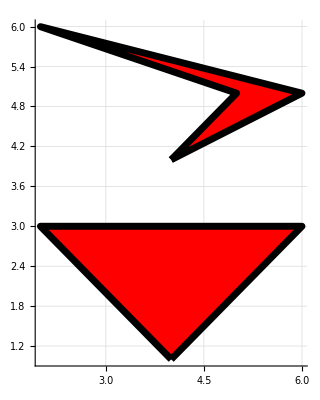

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
fig2=newGeo[{1,{{2,5},{4,6},{0,7},{3,6}}}];
fig12={fig1,fig2};
tra3[fig12,{2,-1}]//toGL//gr1
```

### ROTATION

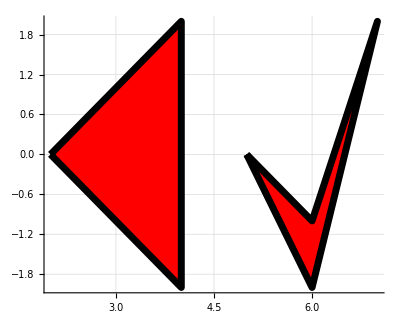

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
fig2=newGeo[{1,{{2,5},{4,6},{0,7},{3,6}}}];
fig12={fig1,fig2};
rot3[fig12,{3/2 Pi,{1,1}}]//toGL//gr1
```

### REFLECTION

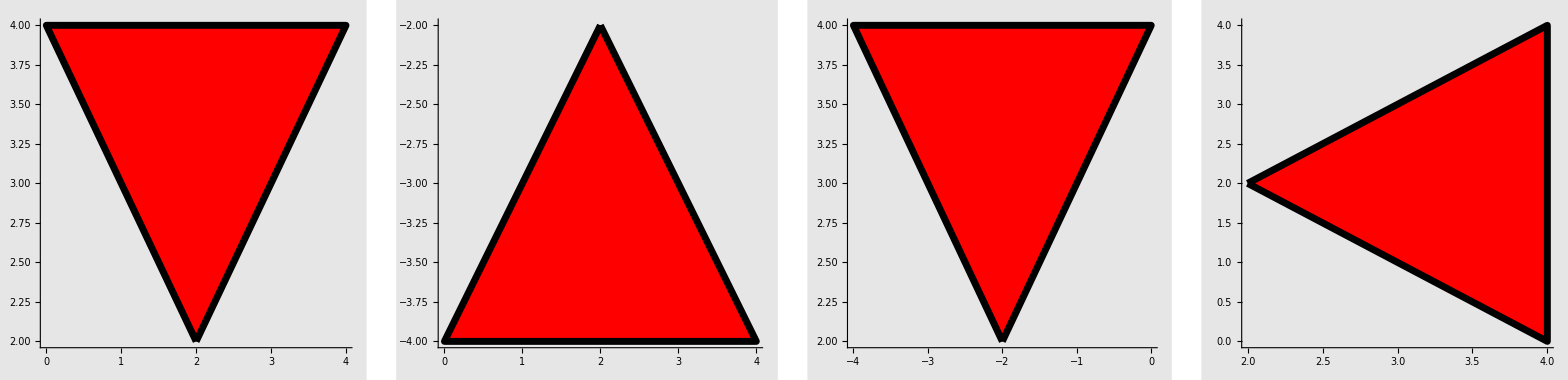

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
fig2=newGeo[{1,{{2,5},{4,6},{0,7},{3,6}}}];
fig12={fig1,fig2};
GraphicsRow[
{fig1//toGL//gr2,
ref3[fig1,{{0,1},{0,0}}]//toGL//gr2 (* Reflection in X-axis *),
ref3[fig1,{{1,0},{0,0}}]//toGL//gr2 (* Reflection in Y-axis *),
ref3[fig1,{{-1,1},{0,0}}]//toGL//gr2 (* Reflection in line Y=X *)}
]
```

### CONJUGATION

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
fig2=newGeo[{1,{{2,5},{4,6},{0,7},{3,6}}}];
fig12={fig1,fig2};
cnj3[cnj3[fig1]]//toGL//gr1
```

-Graphics-

### SCALING

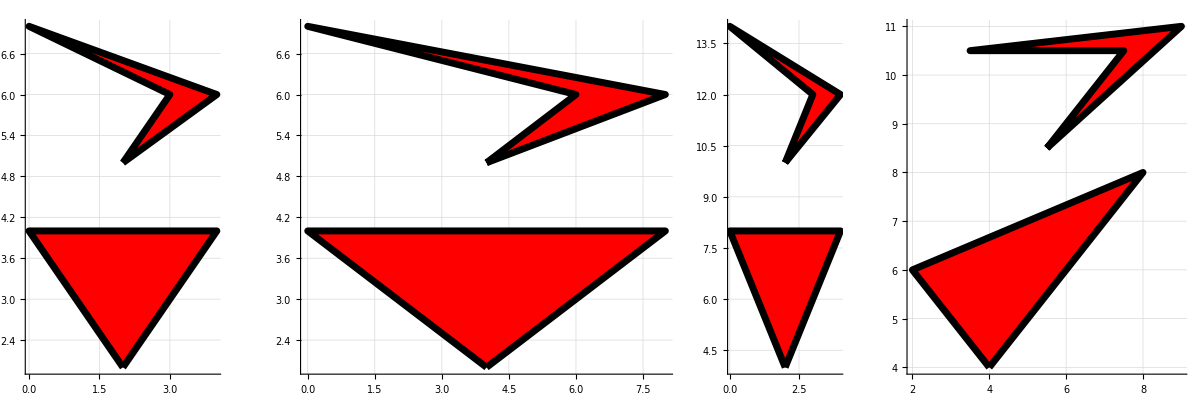

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
fig2=newGeo[{1,{{2,5},{4,6},{0,7},{3,6}}}];
fig12={fig1,fig2};
GraphicsRow[
{fig12//toGL//gr1,
sca3[fig12,{2,{1,0}}]//toGL//gr1,
sca3[fig12,{2,{0,1}}]//toGL//gr1,
sca3[fig12,{2,{1,1}}]//toGL//gr1}
]
```

## Property Updates

### FACE COLOR

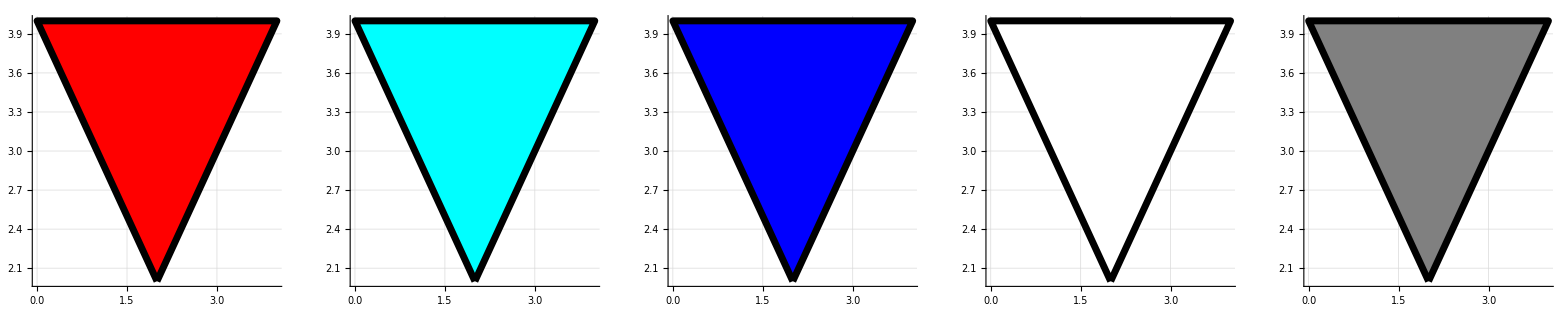

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
GraphicsRow[
{fig1//toGL//gr1,
repCol[fig1,{Cyan}]//toGL//gr1,
repCol[fig1,{Blue}]//toGL//gr1,
repCol[fig1,{White}]//toGL//gr1,
repCol[fig1,{Gray}]//toGL//gr1
}
]
```

### LINE COLOR

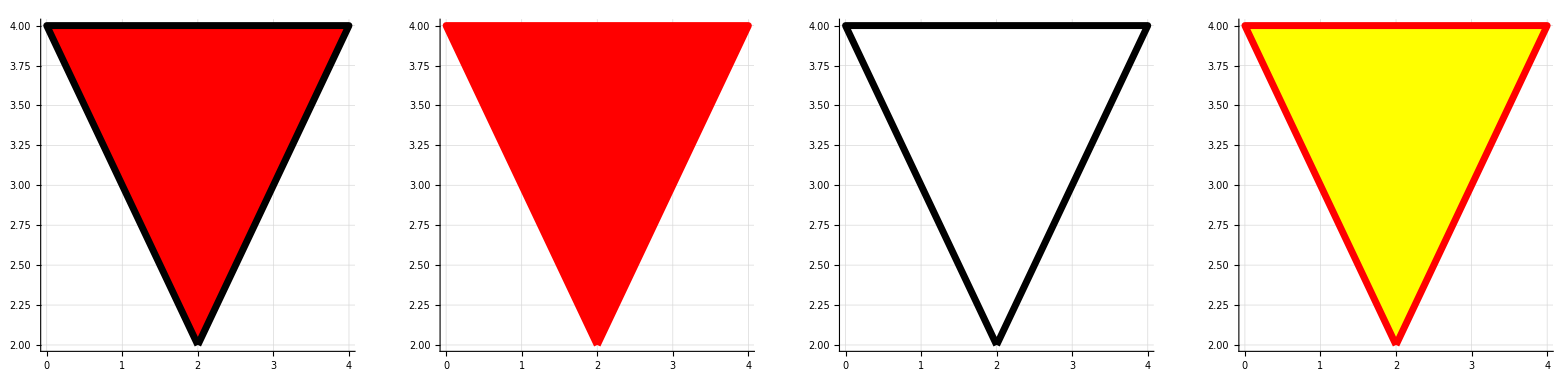

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
GraphicsRow[
{fig1//toGL//gr1,
repLineCol[fig1,{Red}]//toGL//gr1,
repCol[fig1,{White}]//toGL//gr1,
repLineCol[repCol[fig1,{Yellow}],{Red}]//toGL//gr1
}
]
```